```mathematica
<<Units`
ppgfttoPSI=0.0519481;
```

```mathematica
LinearEq[pt1_,pt2_]:=Block[{y,x,temp,temp2,temp3},
pt1[[1]]+(y-pt1[[2]])(pt2[[1]]-pt1[[1]])/(pt2[[2]]-pt1[[2]])
];

Interpolate[ycoord_,data_]:=Block[{f,i,y},
For[i=1,i< Length[data],i++,
If[Abs[data[[i,2]]]≤Abs[ycoord]≤ Abs[data[[i+1,2]]],
f=LinearEq[data[[i]],data[[i+1]]];
Return[f/.y->ycoord];
];
];
];
```

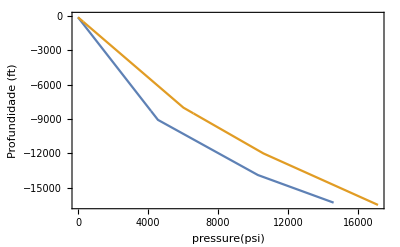

```mathematica
dataporepressure={{8.33,-100},{9.7,-9066},{14.25,-13885},{17.25,-16300}};
PtsFracPressure={{9,-100},{14.5,-6025.97},{17,-12000},{20,-16500}};
dataporepressure={{0,-100},{4568.32,-9066},{10278.50,-13885},{14606.48,-16300}};
PtsFracPressure={{0,-100},{6025.97,-8000},{10597.39,-12000},{17142.84,-16500}};
tabpore=Table[{Interpolate[y,dataporepressure],y},{y,-16300,0}];
tabfrac=Table[{Interpolate[y,PtsFracPressure],y},{y,-16500,0}];
ListLinePlot[{tabpore,tabfrac},Frame->True,FrameLabel->{{" Profundidade (ft) "," "},{"pressure(psi)"," Janela Operacional "}},LabelStyle->Directive[Bold,14],Axes->None]
```

```mathematica
MakeCompatibleSizeVectors[refinedvec_,coarsevecl_,coarsevecvar_]:=Block[{newvec,y0,y1,x0,x1,counter,i},
newvec={};
counter=1;
If[Length[coarsevecl]!=Length[coarsevecvar],
Print["Não é possível realizar o refinamento, os vetores coarse devem ter o mesmo tamanho."];
];
For[i=1,i<Length[coarsevecl],i++,
(*If[i>=Length[coarsevecvar],Break[]];*)
y0=coarsevecvar[[i]];
y1=coarsevecvar[[i+1]];
x0=coarsevecl[[i]];
x1=coarsevecl[[i+1]];
While[(coarsevecl[[i]]<=refinedvec[[counter]]<=coarsevecl[[i+1]])&&counter<Length[refinedvec],
AppendTo[newvec,N[(y1-y0)/(x1-x0) (refinedvec[[counter]]-x0)+y0]];
counter++;
];
If[i==Length[coarsevecl]-1,AppendTo[newvec,N[(y1-y0)/(x1-x0) (refinedvec[[counter]]-x0)+y0]]];
];
newvec//N
]
```

```mathematica
(*refina de n divisões de refl até lf*)
refine[l0_,lf_,refl_,n_,nreffull_]:=Block[{dref,standardref=nreffull,refinedvec,lastcoarsedata,i},
refinedvec=Table[dl//N,{dl,l0,refl,(refl-l0)/standardref}];
lastcoarsedata=refl;
If[Abs[lf-refl]<10^-8,
dref=(lf-l0)/n;
refinedvec={};
lastcoarsedata=l0;
,
dref=(lf-refl)/n;
lastcoarsedata=refl;
];

For[i=1,i≤n,i++,
AppendTo[refinedvec,lastcoarsedata//N];
lastcoarsedata+=dref;
];
AppendTo[refinedvec,N[lf]];
refinedvec//N
]
```

Dado PI e PO, rint e rext, faz o cálculo da tensão radial e tangencial

```mathematica
ComputeRadialAndTangetialStress[r_,ri_,re_,PI_,PO_]:=Block[{sigr,sigtheta},
sigr=(PI (r^2-re^2) ri^2+PO re^2 (-r^2+ri^2))/(r^2 (re^2-ri^2));
sigtheta=(PI(r^2+re^2) ri^2-PO re^2 (r^2+ri^2))/(r^2 (re^2-ri^2));
{sigr,sigtheta}//N
];
ComputeRadialAndTangetialStress2[r_,ri_,re_,PI_,PO_,FZ_]:=Block[{ez,sigrr,sigtt,sigzz,a,b,Pa,Pb,nu=0.30,young=3 10^7},
a=ri;
b=re;
Pa=PI;
Pb=PO;
ez=FZ/(Pi young(b^2-a^2))-(2nu)/young(Pa a^2 -Pb b^2)/(b^2-a^2);
sigrr=(Pa a^2 -Pb b^2)/(b^2-a^2)-(a^2 b^2 (Pa-Pb))/((b^2-a^2)r^2);
sigtt=(Pa a^2 -Pb b^2)/(b^2-a^2)+(a^2 b^2 (Pa-Pb))/((b^2-a^2)r^2);
sigzz=2 nu (Pa a^2 -Pb b^2)/(b^2-a^2)+young ez;
{sigrr,sigtt,sigzz}//N
];
(*di=12.376;
de=14;
{sigr,sigt,sigz}=ComputeRadialAndTangetialStress2[di/2 ,di/2,de/2,8237,3629,1.312705856587157*^6]
sigz Pi/4( de^2-di^2)*)
```

Dado dint, dext, PI e PO, faz o cálculo da tensão axial (TA) devido ao efeito poisson (Balão)

```mathematica
ComputeFballoning[di_,de_,Pint_,Pext_,nu_]:=Block[{sigr,sigt,Fballoning},
{sigr,sigt}=ComputeRadialAndTangetialStress[di/2 ,di/2,de/2,Pint,Pext];
Fballoning=nu(sigr+sigt)Pi/4( de^2-di^2);
Fballoning//N
];
```

```mathematica
ComputeFtemperature[de_,di_,TM_,TPM_]:=Block[{young = 3 10^7,alfa=6.9 10^-6,ΔT,T1,f,fp,T2,Ftemperature},
ΔT= (TPM-TM) ;
Ftemperature=-young alfa ΔT Pi/4(de^2-di^2);
Ftemperature//N
]
```

```mathematica
ComputeFBend[de_,di_,θ_]:=Block[{young = 3. 10^7,area,Fbend},
area=Pi/4. (de^2. -di^2.);
Fbend=Pi young de θ/(100. 360. 12.) area;
Fbend//N(*resultado em lb*)
]
```

```mathematica
di=19.124;
de=20;
ComputeFBend[de,di,2]
```

234901.

```mathematica
ComputeInitialForce[InternalPressIni_,ExternalPressIni_,Lvec_,PipeData_]:=Block[{Lcement,Fpiston,sz,di,de,alfa,nu,young,w,Ai,Ao,i,lacum=0.,Fi},
{di,de,alfa,nu,young,w,Lcement}=PipeData;(*dados do tubular*)
Ai=Pi/4 di^2;(*área interna*)
Ao=Pi/4 de^2;(*área externa*)
sz=Length[Lvec];
Fi=Table[0,{sz}];
Fpiston=(InternalPressIni[[sz]] Ai-ExternalPressIni[[sz]] Ao);(*Força Pistão*)
Fi[[sz]]=Fpiston;
For[i=sz-1,i≥1,i--,
lacum+=(-Lvec[[i]]+Lvec[[i+1]]);
Fi[[i]]=Fpiston+w lacum;(*Força axial inicial total*)
];

Fi//N
]
```

```mathematica
ComputeInitialForce[InternalPressIni_,ExternalPressIni_,Lvec_,PipeData_,doglegdata_]:=Block[{Lcement,Fpiston,sz,di,de,alfa,nu,young,w,Ai,Ao,i,lacum=0.,Fi},
{di,de,alfa,nu,young,w,Lcement}=PipeData;(*dados do tubular*)
Ai=Pi/4 di^2;(*área interna*)
Ao=Pi/4 de^2;(*área externa*)
sz=Length[Lvec];
Fi=Table[0,{sz}];
Fpiston=(InternalPressIni[[sz]] Ai-ExternalPressIni[[sz]] Ao);(*Força Pistão*)
Fi[[sz]]=Fpiston;
For[i=sz-1,i≥1,i--,
lacum+=(-Lvec[[i]]+Lvec[[i+1]]);
Fi[[i]]=Fpiston+w lacum+ComputeFBend[de,di,doglegdata[[i]]];(*Força axial inicial total*)
];

Fi//N
]
```

```mathematica
ComputeForces[InternalPressinitial_,ExternalPressinitial_,InternalPressKick_,ExternalPressKick_,Ti_,Tf_,Lvec_,PipeData_]:=Block[{Lcement,Fi,Fballoning,Ftemp,flag,Ffreemean,sz,di,de,alfa,nu,young,w,Ai,Ao,i,lacum=0.,Ffinal,ΔInternalPress,ΔExternalPress},
(*Calcula a força devido as condições iniciais*)
Fi=ComputeInitialForce[InternalPressinitial,ExternalPressinitial,Lvec,PipeData];
ΔInternalPress=InternalPressKick-InternalPressinitial;
ΔExternalPress=ExternalPressKick-ExternalPressinitial;
Print["Length[InternalPressKick] = ",Length[InternalPressKick]];
Print["Length[InternalPressinitial] = ",Length[InternalPressinitial]];
Print["Length[ExternalPressKick] = ",Length[ExternalPressKick]];
Print["Length[ExternalPressinitial] = ",Length[ExternalPressinitial]];
{di,de,alfa,nu,young,w,Lcement}=PipeData;
Ai=Pi/4 di^2;
Ao=Pi/4 de^2;
sz=Length[ΔInternalPress];
Ffreemean=0.;
(*Calcula a força devido ao efeito poisson ou balão*)
Fballoning=ComputeFballoning[di,de,#1,#2,nu]&[ΔInternalPress,ΔExternalPress];
(*Calcula a força devido ao efeito térmico*)
Ftemp=ComputeFtemperature[de,di,#1,#2]&[Ti,Tf];
Ffinal=Table[0,{sz}];
Ffinal[[sz]]=Fi[[sz]]+Fballoning[[sz]]+Ftemp[[sz]];
For[i=sz-1,i≥1,i--,
lacum+=Lvec[[i+1]]-Lvec[[i]];
If[lacum-(Lvec[[sz]]-Lcement)<=0,
(*Trecho Cimentado*)
Ffinal[[i]]=Fi[[i]]+Fballoning[[i]]+Ftemp[[i]];
flag=True;
,
(*Trecho Livre*)
If[flag==True,
(*No primeiro passo do trecho livre calcula a média das forças de temperatura e balão somente do trecho livre*)
Ffreemean=(Sum[Fballoning[[j]],{j,1,i}]+Sum[Ftemp[[j]],{j,1,i}])/i;
flag=False;
];
Ffinal[[i]]=Ffreemean+Fi[[i]];
];
];
{Fi,Ffinal}//N
]
```

```mathematica
ComputeForces[InternalPressinitial_,ExternalPressinitial_,InternalPressKick_,ExternalPressKick_,Ti_,Tf_,Lvec_,PipeData_,doglegdata_]:=Block[{Lcement,Fi,Fballoning,Ftemp,flag,Ffreemean,sz,di,de,alfa,nu,young,w,Ai,Ao,i,lacum=0.,Ffinal,ΔInternalPress,ΔExternalPress},
(*Calcula a força devido as condições iniciais*)
Fi=ComputeInitialForce[InternalPressinitial,ExternalPressinitial,Lvec,PipeData,doglegdata];
ΔInternalPress=InternalPressKick-InternalPressinitial;
ΔExternalPress=ExternalPressKick-ExternalPressinitial;
Print["Length[InternalPressKick] = ",Length[InternalPressKick]];
Print["Length[InternalPressinitial] = ",Length[InternalPressinitial]];
Print["Length[ExternalPressKick] = ",Length[ExternalPressKick]];
Print["Length[ExternalPressinitial] = ",Length[ExternalPressinitial]];
{di,de,alfa,nu,young,w,Lcement}=PipeData;
Ai=Pi/4 di^2;
Ao=Pi/4 de^2;
sz=Length[ΔInternalPress];
Ffreemean=0.;
(*Calcula a força devido ao efeito poisson ou balão*)
Fballoning=ComputeFballoning[di,de,#1,#2,nu]&[ΔInternalPress,ΔExternalPress];
(*Calcula a força devido ao efeito térmico*)
Ftemp=ComputeFtemperature[de,di,#1,#2]&[Ti,Tf];
Ffinal=Table[0,{sz}];
Ffinal[[sz]]=Fi[[sz]]+Fballoning[[sz]]+Ftemp[[sz]];
For[i=sz-1,i≥1,i--,
lacum+=Lvec[[i+1]]-Lvec[[i]];
If[lacum-(Lvec[[sz]]-Lcement)<=0,
(*Trecho Cimentado*)
Ffinal[[i]]=Fi[[i]]+Fballoning[[i]]+Ftemp[[i]];
flag=True;
,
(*Trecho Livre*)
If[flag==True,
(*No primeiro passo do trecho livre calcula a média das forças de temperatura e balão somente do trecho livre*)
Ffreemean=(Sum[Fballoning[[j]],{j,1,i}]+Sum[Ftemp[[j]],{j,1,i}])/i;
flag=False;
];
Ffinal[[i]]=Ffreemean+Fi[[i]];
];
];
{Fi,Ffinal}//N
]
```

Calcula a resistência do tubular à ruptura e ao colapso de acordo com a API BUL 5C3

```mathematica
ComputePipeStrength[siga_,sigy_,de_,di_,young_,nu_]:=Block[{t=(de-di)/2,BurstStrength, ColapseStrength,dt,Ypa,A,B,C,F,G,range1,range2,range3},
BurstStrength=0.875 2 sigy/(de/t);
dt=de/t;
Ypa=sigy (Sqrt[1-3/4 (siga/sigy)^2]-1/2 siga/sigy);
A=2.8762+0.10679 10^-5 Ypa+0.21301 10^-10 Ypa^2-0.53132 10^-16 Ypa^3;
B=0.026233+0.50609 10^-6 Ypa;
C=-465.93+0.030867 Ypa-0.10483 10^-7 Ypa^2+0.36989 10^-13 Ypa^3;
F=(46.95 10^6 ((3(B/A))/(2+B/A))^3)/(Ypa((3(B/A))/(2+B/A)-B/A)(1-(3(B/A))/(2+B/A))^2);
G=F B/A;
range1=(2+B/A)/(3 B/A);

If[dt≥ range1,

ColapseStrength=(2 young)/(1-nu^2) 1/(dt(dt-1)^2);
];
range2=(Ypa(A-F))/(C+Ypa(B-G));
If[range2≤ dt≤ range1,

ColapseStrength= (F/dt-G)Ypa;
];
range3=(Sqrt[(A-2)^2+8(B+C/Ypa)]+(A-2))/(2(B+C/Ypa));
If[(range3≤ dt≤ range2),

ColapseStrength=Ypa (A/dt-B)-C;
];

If[dt≤ range3,

ColapseStrength=2Ypa (dt-1)/dt^2;
];
{BurstStrength,ColapseStrength}//N
];
```

Calcula a tensão de von Mises

```mathematica
ComputeRadialAndTangetialStress[r_,ri_,re_,PI_,PO_]:=Block[{sigr,sigtheta},
sigr=(PI (r^2-re^2) ri^2+PO re^2 (-r^2+ri^2))/(r^2 (re^2-ri^2));
sigtheta=(PI(r^2+re^2) ri^2-PO re^2 (r^2+ri^2))/(r^2 (re^2-ri^2));
{sigr,sigtheta}//N
];
```

```mathematica
ComputeVonMises[sigr_,sigt_,siga_]:=Block[{sig,S,J2,vm,teste},
sig={{sigr,0,0},{0,sigt,0},{0,0,siga}};

S=sig-1/3 Tr[sig] IdentityMatrix[3];
J2=1/2 Tr[S.S];
Sqrt[3 J2]
];
```

1.3 Pressão resistente de Klever Stewart

```mathematica
ComputeBurstResistance[n_,de_,t_,fu_,sa_,po_]:=Block[{a,kdr,kr,puts,pref,Futs,pfactor,pfactorNeck,pM,pBurstKS,pburst},
kdr=0.5^(n+1)+(1/√3)^(n+1);
kr=(4^(1-n)-1)*3^(n-1);
puts=(2 kdr t fu)/(de- t);
pref=(0.5^n*puts)/2(((2/√3)^(n+1))+1);
Futs=Pi t  fu(de-t);
pfactor=Sqrt[1-kr*(sa/fu)^2];
a=(1-sa^2/fu^2)/(-3^(1-n)+4^(1-n));
If[sa<=fu,a=(1-sa^2/fu^2)/(-3^(1-n)+4^(1-n)),a=0];
pfactorNeck=Sqrt[a];
pM=pref pfactor;
pBurstKS=po+Min[pM,(pM+0.5^n puts)/2];
If[sa/fu≤ ((√3)/2)^(1-n),
If[pM≤ (pM+0.5^n puts)/2,
pburst=po+pM;
,
pburst= po+(pM+0.5^n puts)/2;
],
pburst=po+pref*pfactorNeck;
];
pburst//N
];
```

```mathematica
(*ComputeBurstResistance[n_,de_,t_,fu_,sa_,po_]:=Block[{kdr,kr,puts,pref,Futs,pfactor,pfactorNeck,pM,pBurstKS,pburst},
kdr=0.5^(n+1)+(1/√3)^(n+1);
kr=(4^(1-n)-1)*3^(n-1);
puts=(2 kdr t fu)/(de- t);
pref=(0.5^n*puts)/2(((2/√3)^(n+1))+1);
Futs=Pi t  fu(de-t);
pfactor=Sqrt[1-kr*(sa/fu)^2];
pfactorNeck=√((1-sa^2/fu^2)/(-3^(1-n)+4^(1-n)));
pM=pref pfactor;
pBurstKS=po+Min[pM,(pM+0.5^n puts)/2];
pBurstKS

];*)
```

1.3 Pressão resistente de Klever Tamano

```mathematica
(*Hfunc[ov_,ec_,rs_,fy_]:=Max[0,0.127 ov+0.0039ec+0.440 rs/fy];
Hfunc[ov_,ec_,rs_]:=Max[0,0.127 ov+0.0039ec-0.440 rs];
ComputeColapseStrengthKT[siga_,sigy_,pi_,d_,t_,young_,nu_,ov_,ec_,rs_]:=Block[{ke=0.855,sol,H,deltapec,deltapy,deltapmises,deltaptresca,ky=0.835,eq,po,Fa,Feff,Fy,Ai,Ao,As,kdr,BurstStrength, ColapseStrength,pyc,pec,pym,xi,Si,dt,c,val},

deltaptresca=ky 2 sigy t/(d-t);
deltapmises=Sqrt[(ky(4./√3.)sigy t/(d-t))^2 (1.-(siga/(ky sigy))^2)];
deltapy=Min[(deltapmises+deltaptresca)/2,deltapmises];
(*deltapy=(deltapmises+deltaptresca)/2;*)
deltapec=ke (2. young)/(1.-nu^2)1./((d/t)(d/t-1.)^2);
H=Hfunc[ov,ec,rs];
ColapseStrength=pi+(2. deltapy deltapec)/(deltapy+deltapec+Sqrt[(deltapy-deltapec)^2 +4. H deltapy deltapec]);
ColapseStrength

]*)
```

```mathematica
(*Hfunc[ov_,ec_,rs_,fy_]:=Max[0,0.127 ov+0.0039ec+0.440 rs/fy];
Hfunc[ov_,ec_,rs_]:=Max[0,0.127 ov+0.0039ec-0.440 rs];
ComputeColapseStrengthKT[siga_,sigy_,pi_,d_,t_,young_,nu_,ov_,ec_,rs_]:=Block[{i,initialguess,min,tabguess,MisesEq,ke=0.825,sol,H,deltapec,deltapy,deltapmises,deltaptresca,ky=0.855,eq,po,Fa,Feff,Fy,Ai,Ao,As,kdr,BurstStrength, ColapseStrength,pyc,pec,pym,xi,Si,dt,c,val},
deltaptresca=ky 2 sigy t/(d-t);
MisesEq=pi-po+2.3094010767585034 √((ky^2 sigy^2 t^2 (1.-((d^2 (pi-po)-4 d (pi+siga) t+4 (pi+siga) t^2)^2)/(16 ky^2 sigy^2 (d-t)^2 t^2)))/(d-t)^2);
tabguess=Table[{i,MisesEq/.po->i},{i,1000,20000,500}];
min=Min[Transpose[Abs[tabguess]][[2]]];
initialguess=0.;
For[i=1,i≤Length[tabguess],i++,If[Abs[tabguess[[i,2]]]==min,initialguess=tabguess[[i,1]]]];
If[initialguess≤2000,
sol=initialguess;
,
sol=FindRoot[MisesEq,{po,initialguess},MaxIterations->30][[1,2]];
];
deltapmises=sol-pi;

deltapy=Min[(deltapmises+deltaptresca)/2,deltapmises];
deltapec=ke (2. young)/(1.-nu^2)1./((d/t)(d/t-1.)^2);
H=Hfunc[ov,ec,rs];
ColapseStrength=pi+(2. deltapy deltapec)/(deltapy+deltapec+Sqrt[(deltapy-deltapec)^2 +4. H deltapy deltapec]);
ColapseStrength

]*)
```

```mathematica
(*Hfunc[ov_,ec_,rs_,fy_]:=Max[0,0.127 ov+0.0039ec+0.440 rs/fy];
Hfunc[ov_,ec_,rs_]:=Max[0,0.127 ov+0.0039ec-0.440 rs];
ComputeColapseStrengthKT[siga_,sigy_,pi_,d_,t_,young_,nu_,ov_,ec_,rs_]:=Block[{i,initialguess,min,tabguess,MisesEq,ke=0.825,sol,H,deltapec,deltapy,deltapmises,deltaptresca,ky=0.855,eq,po,Fa,Feff,Fy,Ai,Ao,As,kdr,BurstStrength, ColapseStrength,pyc,pec,pym,xi,Si,dt,c,val},
deltaptresca=ky 2 sigy t/(d-t);
MisesEq=pi-po+2.3094010767585034 √((ky^2 sigy^2 t^2 (1.-((d^2 (pi-po)-4 d (pi+siga) t+4 (pi+siga) t^2)^2)/(16 ky^2 sigy^2 (d-t)^2 t^2)))/(d-t)^2);
tabguess=Table[{i,MisesEq/.po->i},{i,1000,20000,500}];
(*Print["tabguess = ",tabguess];*)

min=Min[Transpose[Abs[tabguess]][[2]]];
initialguess=0.;
For[i=1,i≤Length[tabguess],i++,If[Abs[tabguess[[i,2]]]==min,initialguess=tabguess[[i,1]]]];
(*Print["initialguess = ",initialguess];*)
sol=FindRoot[MisesEq,{po,initialguess},MaxIterations->100][[1,2]];
(*sol=FindRoot[MisesEq,{po,initialguess},MaxIterations->30][[1,2]];*)
(*Print["sol = ",sol];*)

sol=initialguess;
deltapmises=sol-pi;

deltapy=Min[(deltapmises+deltaptresca)/2,deltapmises];
deltapec=ke (2. young)/(1.-nu^2)1./((d/t)(d/t-1.)^2);
H=Hfunc[ov,ec,rs];
ColapseStrength=pi+(2. deltapy deltapec)/(deltapy+deltapec+Sqrt[(deltapy-deltapec)^2 +4. H deltapy deltapec]);
ColapseStrength

]*)
```

```mathematica
(*ComputeNumericalGradKT[Vars_,Xvec_]:=Block[{vars,guess,dx=0.001,xvecn,xvecn1,dgdx,derivative,i,X1,X2,X3,X4,X5,X6,X7,X8,X9,NofD,nYieldStrength,PintofD,PextofD,nDe,nt,nYoung,nNu},
vars={NofD,nYieldStrength,PintofD,PextofD,nDe,nt,nYoung,nNu};
Gx[vars_,xvec_]:=xvec[[1]]*ComputeColapseStrengthKT[vars[[1]]*xvec[[7]],vars[[2]]*xvec[[2]],vars[[3]]*xvec[[8]],vars[[5]],vars[[6]]*xvec[[3]],vars[[7]],vars[[8]],xvec[[4]],xvec[[5]],xvec[[6]]]-(vars[[4]]*xvec[[9]]-vars[[3]]*xvec[[8]]);
xvecn=Xvec;
derivative=Table[0,{Length[xvecn]}];
For[i=1,i≤Length[xvecn],i++,
xvecn1=xvecn;
xvecn1[[i]]+=dx;
dgdx=(Gx[Vars,xvecn1]-Gx[Vars,xvecn])/dx;
derivative[[i]]=dgdx;
];
{Gx[Vars,xvecn],derivative}
]*)
```

```mathematica
ComputeNumericalGradKT[Vars_,Xvec_]:=Block[{dx=0.001,xvecn,xvecn1,dgdx,derivative,i,NofD,nYieldStrength,PintofD,PextofD,nDe,nt,nYoung,nNu},
{NofD,nYieldStrength,PintofD,PextofD,nDe,nt,nYoung,nNu}=Vars;
Gx[xvec_]:=xvec[[1]]*ComputeColapseStrengthKT[NofD*xvec[[7]],nYieldStrength*xvec[[3]],PintofD*xvec[[8]],nDe,nt*xvec[[2]],nYoung,nNu,xvec[[4]],xvec[[5]],xvec[[6]]]-(PextofD*xvec[[9]]-PintofD*xvec[[8]]);
xvecn=Xvec;
derivative=Table[0,{Length[xvecn]}];

For[i=1,i≤Length[xvecn],i++,
xvecn1=xvecn;
xvecn1[[i]]+=dx;
dgdx=(Gx[xvecn1]-Gx[xvecn])/dx;
derivative[[i]]=dgdx;
];
{Gx[xvecn],derivative}
]
```

Calcula os fatores de segurança

```mathematica
ComputeSafetyFactors[PipeData_,AxialForce_,Pint_,Pext_,ov_,ec_,rs_]:=Block[{KTStress,KSstress,KSSF={},KTSF={},APISF={}, BarlowSF={},i,barlow,api,de,di,young,nu,weigthperfeet,L1,L2,pipe=1,sigy,VMSF={},sigr,sigt,area,VMStress},

{de,di,young,nu,weigthperfeet,L1,L2,sigy}=PipeData[[pipe]];
For[i=Length[Pint]-1,i>1,i--,
If[L1>Pint[[i,2]],
pipe++;
{de,di,young,nu,weigthperfeet,L1,L2,sigy}=PipeData[[pipe]];
];
{sigr,sigt}=ComputeRadialAndTangetialStress[di/2,di/2,de/2,Pint[[i,1]],Pext[[i,1]]];
area=Pi/4 (de^2 -di^2);


VMStress=ComputeVonMises[sigr,sigt,AxialForce[[i,1]]/area];
KSstress=ComputeBurstResistance[1,de,0.5(de -di),sigy,AxialForce[[i,1]]/area,Pext[[i,1]]];
KTStress=ComputeColapseStrengthKT[AxialForce[[i,1]]/area,sigy,Pint[[i,1]],de,0.5(de -di),young,nu,ov,ec,rs];
api=ComputePipeStrength[AxialForce[[i,1]]/area,sigy,de,di,young,nu];
If[burst==True,
deltap=(Pint[[i,1]]-Pext[[i,1]]);
,
deltap=(-Pint[[i,1]]+Pext[[i,1]]);
];
AppendTo[BarlowSF,{api[[1]]/deltap,-Pint[[i,2]]}];
AppendTo[APISF,{api[[2]]/deltap,-Pint[[i,2]]}];
AppendTo[VMSF,{sigy/VMStress,-Pint[[i,2]]}];
AppendTo[KSSF,{KSstress/deltap,-Pint[[i,2]]}];
AppendTo[KTSF,{KTStress/deltap,-Pint[[i,2]]}];
];
{BarlowSF,APISF,VMSF,KSSF,KTSF}
];
```

# MUD DROP DUE TO LOST RETURNS

# -Graphics-

Length[InternalPressKick] = 16

Length[InternalPressinitial] = 16

Length[ExternalPressKick] = 16

Length[ExternalPressinitial] = 16

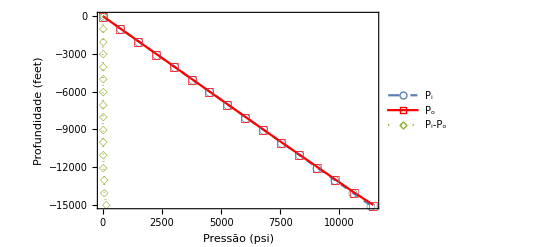

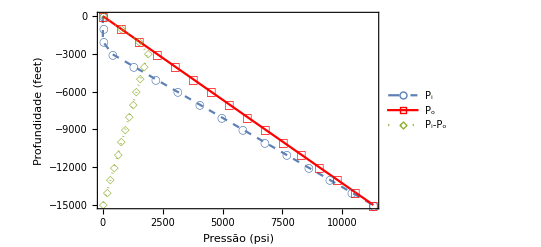

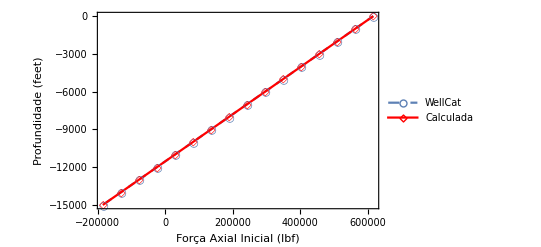

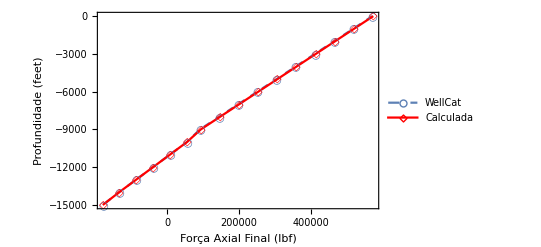

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

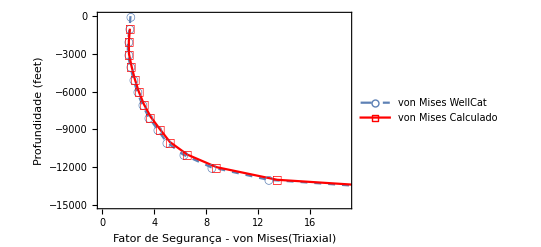

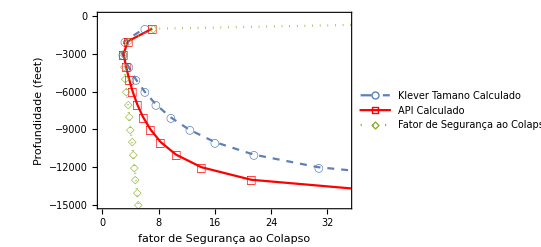

```mathematica
burst=False;
lvec={0,100,951,1901,2100,2100,2581,2851,2995,3409,3801,3823,4237,4651,4751,5065,5479,5700,5893,6307,6650,6721,7135,7549,7600,7963,8377,8550,8791,9066,9205,9500,9500,9618,9700,9700,9950,10032,10400,10446,10850,10860,11274,11300,11688,11750,12102,12200,12516,12650,12930,13100,13344,13550,13758,13885,14000,14100,14172,14200,14300,14400,14500,14586,14600,14700,14800,14900,15000};
InternalPressLostCirc={1.36,1.36,1.36,1.37,1.37,1.37,1.37,246.55,377.70,754.03,1110.09,1130.36,1506.70,1883.03,1973.64,2259.36,2635.70,2837.18,3012.03,3388.36,3700.72,3764.69,4141.03,4517.36,4564.27,4893.69,5270.03,5427.82,5646.36,5896.81,6022.69,6291.27,6291.45,6399.03,6473.09,6473.27,6700.45,6775.36,7109.54,7151.69,7518.63,7528.02,7904.36,7927.72,8280.69,8336.81,8657.02,8745.90,9033.36,9154.99,9409.69,9564.08,9786.02,9973.17,10162.35,10277.71,10382.26,10473.17,10538.69,10564.08,10654.99,10745.90,10836.81,10915.02,10927.72,11018.63,11109.53,11200.44,11291.26};
ExternalPressLostCirc={0.00,74.49,715.43,1430.94,1580.91,1581.06,1943.30,2146.45,2255.12,2566.93,2861.96,2878.76,3190.58,3502.39,3577.47,3814.21,4126.04,4292.98,4437.85,4749.67,5008.49,5061.49,5373.31,5685.13,5724.00,5996.95,6308.76,6439.51,6620.59,6828.10,6932.40,7154.94,7155.92,7245.04,7306.41,7306.57,7494.80,7556.87,7833.76,7868.69,8172.72,8180.50,8492.32,8511.68,8804.15,8850.64,9115.96,9189.60,9427.78,9528.56,9739.60,9867.52,10051.41,10206.48,10363.23,10458.82,10545.44,10620.77,10675.05,10696.09,10771.42,10846.74,10922.07,10986.87,10997.39,11072.72,11148.04,11223.37,11298.62};
AxialForceLostCircWellCat={572652,567361,521838,471018,460366,460355,434627,420198,412480,390333,369379,368186,346038,323891,318559,301744,279597,267739,257450,235302,216920,213155,191008,168861,166100,146713,124566,115281,102419,87680,80272,64461,78890,73268,69395,69396,57528,53616,36166,33965,14805,14315,-5338,-6558,-24987,-27917,-44637,-49278,-64289,-70641,-83941,-92002,-103591,-113363,-123240,-129264,-134602,-139149,-142425,-143695,-148241,-152788,-157326,-161215,-161846,-166366,-170886,-175406,-179926};
lvecini={0,951,1901,2100,2100,2851,3801,4751,5700,6650,7600,8550,9500,9500,9501,9700,9700,9950,10400,10850,11300,11750,12200,12650,13100,13550,14000,14100,14200,14300,14400,14500,14600,14700,14800,14900,15000};
AxialForceInitialWellCat={616757,565942,515123,504471,504460,464303,413483,362664,311844,261025,210205,159385,108566,108566,108539,97866,97866,84491,60416,36341,12266,-11809,-35884,-59959,-84034,-108110,-132185,-137535,-142885,-148235,-153585,-158935,-164285,-169635,-174985,-180335,-185685};
AxialForceInitialWellCat=MakeCompatibleSizeVectors[lvec,lvecini,AxialForceInitialWellCat];
InternalPressinitial={0.88,716.30,1431.80,1581.77,1581.92,2147.30,2862.80,3578.30,4293.80,5009.30,5724.80,6440.30,7155.73,7155.88,7156.18,7306.39,7306.54,7494.80,7833.80,8172.70,8511.70,8850.60,9189.60,9528.60,9867.50,10206.50,10545.40,10620.80,10696.10,10771.40,10846.70,10922.10,10997.40,11072.70,11148.00,11223.40,11298.62};
InternalPressinitial=MakeCompatibleSizeVectors[lvec,lvecini,InternalPressinitial];
ExternalPressinitial={0.88,716.30,1431.80,1581.77,1581.92,2147.30,2862.80,3578.30,4293.80,5009.30,5724.80,6440.30,7155.73,7155.88,7156.18,7309.50,7309.65,7501.80,7847.80,8193.75,8539.70,8885.70,9231.70,9577.65,9923.60,10269.60,10615.60,10697.65,10779.70,10861.80,10943.90,11025.95,11108.00,11190.10,11272.20,11354.30,11436.32};
ExternalPressinitial=MakeCompatibleSizeVectors[lvec,lvecini,ExternalPressinitial];
Ti=Table[0,{i,1,Length[lvec]}];
Tf=Table[0,{i,1,Length[lvec]}];


vmsfwellcat={2.172,2.168,2.109,1.994,1.894,1.939,1.964,2.040,2.117,2.122,2.210,2.307,2.331,2.412,2.527,2.593,2.653,2.793,2.921,2.949,3.122,3.318,3.344,3.539,3.793,3.910,4.085,4.305,4.425,4.705,4.488,4.589,4.660,4.660,4.896,4.978,5.385,5.441,5.983,5.998,6.682,6.730,7.542,7.690,8.656,8.969,10.157,10.759,12.286,13.442,15.543,17.903,21.146,23.771,26.723,29.896,32.692,33.922,39.196,46.402,56.813,70.297,73.107,100,100,100,100};
colapsesfwellcat={100,69.549,7.439,3.836,2.883,2.927,2.951,3.020,3.085,3.089,3.159,3.229,3.246,3.300,3.372,3.411,3.445,3.519,3.581,3.594,3.669,3.746,3.756,3.824,3.903,3.936,3.983,4.037,4.065,4.124,4.107,4.130,4.146,4.146,4.195,4.212,4.286,4.295,4.378,4.381,4.462,4.466,4.529,4.539,4.597,4.614,4.668,4.692,4.742,4.772,4.817,4.856,4.895,4.920,4.942,4.962,4.976,4.981,5.001,5.021,5.042,5.059,5.062,5.083,5.103,5.124,5.145};

(*Refinamento da solução*)
refinedl=Table[dl,{dl,0,15000,1000}];
InternalPressinitial=MakeCompatibleSizeVectors[refinedl,lvec,InternalPressinitial];
ExternalPressinitial=MakeCompatibleSizeVectors[refinedl,lvec,ExternalPressinitial];
AxialForceInitialWellCat=MakeCompatibleSizeVectors[refinedl,lvec,AxialForceInitialWellCat];
AxialForceLostCircWellCat=MakeCompatibleSizeVectors[refinedl,lvec,AxialForceLostCircWellCat];
InternalPressLostCirc=MakeCompatibleSizeVectors[refinedl,lvec,InternalPressLostCirc];
ExternalPressLostCirc=MakeCompatibleSizeVectors[refinedl,lvec,ExternalPressLostCirc];
Ti=MakeCompatibleSizeVectors[refinedl,lvec,Ti];
Tf=MakeCompatibleSizeVectors[refinedl,lvec,Tf];

newlvec={0,100,950,1900,2581,2850,2995,3409,3800,3823,4237,4651,4750,5065,5479,5700,5893,6307,6650,6721,7135,7549,7600,7963,8377,8550,8791,9066,9205,9500,9500,9618,9700,9700,9950,10032,10400,10446,10850,10860,11274,11300,11688,11750,12102,12200,12516,12650,12930,13100,13344,13550,13758,13885,14000,14100,14172,14200,14300,14400,14500,14586,14600,14700,14800,14900,15000};




vmsfwellcat=MakeCompatibleSizeVectors[refinedl,newlvec,vmsfwellcat];
colapsesfwellcat=MakeCompatibleSizeVectors[refinedl,newlvec,colapsesfwellcat];

lvec=refinedl;

vmsfwellcatwithl=Table[{vmsfwellcat[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
colapsesfwellcatwithl=Table[{colapsesfwellcat[[i]],-lvec[[i]]},{i,1,Length[lvec]}];


lcimento=9500.01;
di=8.535;
de=9.625;
alfa=6.9 10^-6;
nu=0.30;
young=3 10^7;
weightperfeet=53.5;
sigy=80000;
PipeData={di,de,alfa,nu,young,weightperfeet,lcimento};
{Fi,Ffim}=ComputeForces[InternalPressinitial,ExternalPressinitial,InternalPressLostCirc,ExternalPressLostCirc,Ti,Tf,lvec,PipeData];
ComputedFi=Table[{Fi[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
ComputedFfim=Table[{Ffim[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
WellCatFi=Table[{AxialForceInitialWellCat[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
WellCatFfim=Table[{AxialForceLostCircWellCat[[i]],-lvec[[i]]},{i,1,Length[lvec]}];

InternalPressinitialPlot=Table[{InternalPressinitial[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
ExternalPressinitialPlot=Table[{ExternalPressinitial[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
diffini=Table[{ExternalPressinitial[[i]]-InternalPressinitial[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
InternalPressLostCircPlot=Table[{InternalPressLostCirc[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
ExternalPressLostCircPlot=Table[{ExternalPressLostCirc[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
difffim=Table[{ExternalPressLostCirc[[i]]-InternalPressLostCirc[[i]],-lvec[[i]]},{i,1,Length[lvec]}];


pressaoini=ListLinePlot[{InternalPressinitialPlot,ExternalPressinitialPlot,diffini},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"Pressão (psi)",""}},PlotLegends->{"P_i","P_o","P_i-P_o"},PlotStyle->{Dashed,Red,Dotted},PlotMarkers->{"○", "□", "◇"}]
pressaosobrevi=ListLinePlot[{InternalPressLostCircPlot,ExternalPressLostCircPlot,difffim},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"Pressão (psi)",""}},PlotLegends->{"P_i","P_o","P_i-P_o"},PlotStyle->{Dashed,Red,Dotted},PlotMarkers->{"○", "□", "◇"}]


forcaini=ListLinePlot[{WellCatFi,ComputedFi},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"Força Axial Inicial (lbf)",""}},PlotLegends->{"WellCat","Calculada"},PlotStyle->{Dashed,Red},PlotMarkers->{ "○", "◇"}]
(*Export["C:\\Users\\Diogo\\Dropbox\\figs\\compara05ftcimentofini.jpg",compara,ImageResolution->300]*)

forcafim=ListLinePlot[{WellCatFfim,ComputedFfim},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"Força Axial Final (lbf)",""}},PlotLegends->{"WellCat","Calculada"},PlotStyle->{Dashed,Red},PlotMarkers->{ "○", "◇"},PlotRange->All]

pipedata={de,di,young,nu,weightperfeet};
pipedatavec={
{de,di,young,nu,weightperfeet,lvec[[1]],lvec[[Length[lvec]]],sigy}
};
PiData=Table[{InternalPressLostCirc[[i]],lvec[[i]]},{i,1,Length[lvec]}];
PeData=Table[{ExternalPressLostCirc[[i]],lvec[[i]]},{i,1,Length[lvec]}];
ax=Table[{Ffim[[i]],lvec[[i]]},{i,1,Length[lvec]}];
{barlowsf,apisf,vmsf,kssf,ktsf}=ComputeSafetyFactors[pipedatavec,ax,PiData,PeData,0.217,3.924,-0.237 1.1 sigy];

vmsfplot=ListLinePlot[{vmsfwellcatwithl,vmsf},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"Fator de Segurança - von Mises(Triaxial)",""}},PlotLegends->{"von Mises WellCat","von Mises Calculado"},PlotStyle->{Dashed,Red},PlotMarkers->{"○", "□"}]
kssfplot=ListLinePlot[{ktsf,apisf,colapsesfwellcatwithl},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"fator de Segurança ao Colapso",""}},PlotLegends->{"Klever Tamano Calculado","API Calculado","Fator de Segurança ao Colapso - WellCat"},PlotStyle->{Dashed,Red,Dotted},PlotMarkers->{"○", "□", "◇"}]
```

```mathematica
KTRandomVarsData={{"KTme","NORMAL",0.9991,0.067*0.9991},{"YieldStress","NORMAL",1.1,0.0422*1.1},{"Thickness","NORMAL",1.0069,0.0259*1.0069},{"Ovality","NORMAL",0.217,0.541*0.217},{"Excent","NORMAL",3.924,0.661*3.924},{"Resid. Stress","NORMAL",-0.237,0.332*0.237},{"Nax","NORMAL",1.,0.01},{"Pint","NORMAL",1.,0.01},{"Pext","NORMAL",1.,0.01}};

M=Transpose[KTRandomVarsData][[3]];
SDev=Transpose[KTRandomVarsData][[4]];
distr=Transpose[KTRandomVarsData][[2]];
nvars=Length[M];
RX=IdentityMatrix[nvars];
RVVec=Table[ComputeRandomVarData[distr[[i]],M[[i]],SDev[[i]]],{i,1,nvars}];
sol=ComputeBeta[{PiData,PeData,ax,pipedatavec[[1]]},{RVVec,RX},ComputeNumericalGradKT,"colapso",False];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
(*ComputeBeta[{PiData,PeData,ax,pipedatavec[[1]]},{RVVec,RX},ComputeNumericalGradKT,False]//AbsoluteTiming*)
```

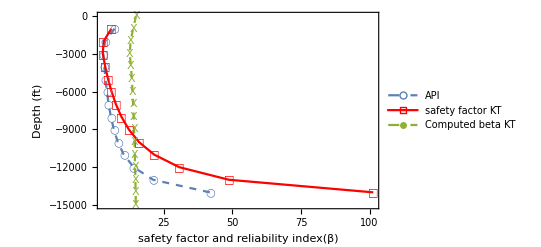

```mathematica
ListLinePlot[{apisf,ktsf,sol},Frame->True,FrameLabel->{{" Depth (ft)","Surface Casing"},{"safety factor and reliability index(β) "," Critical Case: Kick - Assumption: Partial full of gas - Failure check: Klever-Tamano"}},PlotLegends->{"API","safety factor KT ","Computed beta KT"},PlotStyle->{Dashed,Red},PlotMarkers->{"○", "□", "X"},PlotRange->{{0,18},{0,-16000}}]
```

# 7’’ PRODUTICTION TIEBACK Evacuated Casing -Graphics-

```mathematica
burst=False;
lvec={0,100,1480,2960,4440,5920,7400,8880,9066,10360,11840,13320,13885,14800};
InternalPressinitial={0.09,90.91,1345.50,2690.90,4036.40,5381.80,6727.30,8072.70,8241.80,9418.20,10763.60,12109.10,12622.71,13454.41};
ExternalPressinitial={0.09,90.91,1345.45,2690.90,4036.35,5381.80,6727.25,8072.70,8241.79,9418.15,10763.60,12109.05,12622.68,13454.41};
AxialForceInitialWellCat={414946,411149,358709,302469,246229,189989,133749,77509,70441,21269,-34971,-91211,-112681,-147451};


AxialForceEvacuatedCasingWellCat={303906,300110,247670,191430,135190,78950,22710,-33530,-40598,-89770,-146010,-202250,-223720,-258490};
InternalPressEvacuatedCasing={0.00,0.05,0.77,1.54,2.31,3.08,3.84,4.61,4.71,5.38,6.15,6.92,7.21,7.74};
ExternalPressEvacuatedCasing={0.09,90.91,1345.45,2690.91,4036.36,5381.81,6727.27,8072.72,8241.81,9418.17,10763.62,12109.07,12622.71,13454.44};

Ti=Table[0,{i,1,Length[lvec]}];
Tf=Table[0,{i,1,Length[lvec]}];

vmsfwellcat={3.426,3.423,3.228,2.820,2.394,2.032,1.744,1.517,1.492,1.337,1.193,1.075,1.036,0.977};
axialsfwellcat={3.426,3.469,4.204,5.439,7.701,13.187,45.843,31.050,25.644,11.597,7.130,5.148,4.654,4.028};
colapsesfwellcat={100,100,8.646,4.503,3.114,2.414,1.980,1.665,1.631,1.427,1.249,1.110,1.065,0.999};

(*Refinamento da solução*)
(*refinedl=Table[dl,{dl,0,14800,10}];*)
L0=0.;
LF=14800.;
lcimento=14799;
nrefs=100.;
refinedl=refine[L0,LF,14799,50,50];
InternalPressinitial=MakeCompatibleSizeVectors[refinedl,lvec,InternalPressinitial];
ExternalPressinitial=MakeCompatibleSizeVectors[refinedl,lvec,ExternalPressinitial];
AxialForceInitialWellCat=MakeCompatibleSizeVectors[refinedl,lvec,AxialForceInitialWellCat];
AxialForceEvacuatedCasingWellCat=MakeCompatibleSizeVectors[refinedl,lvec,AxialForceEvacuatedCasingWellCat];
InternalPressEvacuatedCasing=MakeCompatibleSizeVectors[refinedl,lvec,InternalPressEvacuatedCasing];
ExternalPressEvacuatedCasing=MakeCompatibleSizeVectors[refinedl,lvec,ExternalPressEvacuatedCasing];
Ti=MakeCompatibleSizeVectors[refinedl,lvec,Ti];
Tf=MakeCompatibleSizeVectors[refinedl,lvec,Tf];




vmsfwellcat=MakeCompatibleSizeVectors[refinedl,lvec,vmsfwellcat];
axialsfwellcat=MakeCompatibleSizeVectors[refinedl,lvec,axialsfwellcat];
colapsesfwellcat=MakeCompatibleSizeVectors[refinedl,lvec,colapsesfwellcat];

lvec=refinedl;



vmsfwellcatwithl=Table[{vmsfwellcat[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
colapsesfwellcatwithl=Table[{colapsesfwellcat[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
axialsfwellcatwithl=Table[{axialsfwellcat[[i]],-lvec[[i]]},{i,1,Length[lvec]}];


Length[vmsfwellcat]
Length[lvec]

di=6.094;
de=7;
alfa=6.9 10^-6;
nu=0.30;
young=3 10^7;
weightperfeet=38;
sigy=95000;
PipeData={di,de,alfa,nu,young,weightperfeet,lcimento};


{Fi,Ffim}=ComputeForces[InternalPressinitial,ExternalPressinitial,InternalPressEvacuatedCasing,ExternalPressEvacuatedCasing,Ti,Tf,lvec,PipeData];
ComputedFi=Table[{Fi[[i]],-lvec[[i]]},{i,1,Length[lvec]-1}];
ComputedFfim=Table[{Ffim[[i]],-lvec[[i]]},{i,1,Length[lvec]-1}];
WellCatFi=Table[{AxialForceInitialWellCat[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
WellCatFfim=Table[{AxialForceEvacuatedCasingWellCat[[i]],-lvec[[i]]},{i,1,Length[lvec]}];


InternalPressinitialPlot=Table[{InternalPressinitial[[i]],-lvec[[i]]},{i,1,Length[lvec]-1}];
ExternalPressinitialPlot=Table[{ExternalPressinitial[[i]],-lvec[[i]]},{i,1,Length[lvec]-1}];
diffini=Table[{ExternalPressinitial[[i]]-InternalPressinitial[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
InternalPressEvacuatedCasingPlot=Table[{InternalPressEvacuatedCasing[[i]],-lvec[[i]]},{i,1,Length[lvec]-1}];
ExternalPressEvacuatedCasingPlot=Table[{ExternalPressEvacuatedCasing[[i]],-lvec[[i]]},{i,1,Length[lvec]-1}];
difffim=Table[{ExternalPressEvacuatedCasing[[i]]-InternalPressEvacuatedCasing[[i]],-lvec[[i]]},{i,1,Length[lvec]-1}];


pressaoini=ListLinePlot[{InternalPressinitialPlot,ExternalPressinitialPlot,diffini},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"Pressão (psi)",""}},PlotLegends->{"P_i","P_o","P_i-P_o"},PlotStyle->{Dashed,Red,Dotted},PlotMarkers->{"○", "□", "◇"}]
pressaosobrevi=ListLinePlot[{InternalPressEvacuatedCasingPlot,ExternalPressEvacuatedCasingPlot,difffim},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"Pressão (psi)",""}},PlotLegends->{"P_i","P_o","P_i-P_o"},PlotStyle->{Dashed,Red,Dotted},PlotMarkers->{"○", "□", "◇"}]

forcaini=ListLinePlot[{WellCatFi,ComputedFi},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"Força Axial Inicial (lbf)",""}},PlotLegends->{"WellCat","Calculada"},PlotStyle->{Dashed,Red},PlotMarkers->{ "○", "◇"},PlotRange->All]
(*Export["C:\\Users\\Diogo\\Dropbox\\figs\\compara05ftcimentofini.jpg",compara,ImageResolution->300]*)

forcafim=ListLinePlot[{WellCatFfim,ComputedFfim},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"Força Axial Final (lbf)",""}},PlotLegends->{"WellCat","Calculada"},PlotStyle->{Dashed,Red},PlotMarkers->{ "○", "◇"},PlotRange->All]

pipedata={de,di,young,nu,weightperfeet};
pipedatavec={
{de,di,young,nu,weightperfeet,lvec[[1]],lvec[[Length[lvec]]],sigy}
};
PiData=Table[{InternalPressEvacuatedCasing[[i]],lvec[[i]]},{i,1,Length[lvec]-1}];
PeData=Table[{ExternalPressEvacuatedCasing[[i]],lvec[[i]]},{i,1,Length[lvec]-1}];
ax=Table[{Ffim[[i]],lvec[[i]]},{i,1,Length[lvec]-1}];
{barlowsf,apisf,vmsf,kssf,ktsf}=ComputeSafetyFactors[pipedatavec,ax,PiData,PeData,0.217,3.924,-0.237 1.1 sigy];
vmsfplot=ListLinePlot[{vmsfwellcatwithl,vmsf},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"Fator de Segurança - von Mises(Triaxial)",""}},PlotLegends->{"von Mises WellCat","von Mises Calculado"},PlotStyle->{Dashed,Red},PlotMarkers->{"○", "□"},PlotRange->All]
ktsfplot=ListLinePlot[{ktsf,apisf,colapsesfwellcatwithl},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"fator de Segurança ao Colapso",""}},PlotLegends->{"Klever Tamano Calculado","API Calculado","Fator de Segurança ao Colapso - WellCat"},PlotStyle->{Dashed,Red,Dotted},PlotMarkers->{"○", "□", "◇"},PlotRange->{{0,4.5},{-14800,0}}]
```

102

102

Length[InternalPressKick] = 102

Length[InternalPressinitial] = 102

Length[ExternalPressKick] = 102

Length[ExternalPressinitial] = 102

-Graphics-

-Graphics-

-Graphics-

-Graphics-

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

-Graphics-

-Graphics-

```mathematica
sol=ComputeBeta[{PiData,PeData,ax,pipedatavec[[1]]},{RVVec,RX},ComputeNumericalGradKT,"colapso",False];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
ListLinePlot[{apisf,ktsf,sol},Frame->True,FrameLabel->{{" Depth (ft)","Surface Casing"},{"safety factor and reliability index(β) "," Critical Case: Kick - Assumption: Partial full of gas - Failure check: Klever-Tamano"}},PlotLegends->{"API","safety factor KT ","reliability indexA(β)"},PlotStyle->{Dashed,Red},PlotMarkers->{"○", "□", "X"},PlotRange->{{0,20},{0,-LF}}]
```

-Graphics-

# -Graphics-

```mathematica
burst=True;
lvec={0,100,1040,1900,1980,2100,2100,2920,3800,3860,4800,5700,5740,6680,7600,7620,8560,9500,9500,9501,9700,9700,9950,10400,10850,11300,11750,12200,12650,13100,13550,14000,14100,14200,14300,14400,14500,14600,14700,14800,14900,15000};
InternalPressinitial={0.05,75.30,783.40,1431.20,1491.40,1581.72,1581.87,2199.50,2862.35,2907.50,3615.60,4293.50,4323.60,5031.70,5724.65,5739.70,6447.80,7155.73,7155.88,7156.18,7306.39,7306.54,7494.80,7833.80,8172.70,8511.70,8850.60,9189.60,9528.60,9867.50,10206.50,10545.40,10620.80,10696.10,10771.40,10846.70,10922.10,10997.40,11072.70,11148.00,11223.40,11298.62};
ExternalPressinitial={0.05,75.30,783.35,1431.20,1491.40,1581.71,1581.87,2199.45,2862.35,2907.50,3615.55,4293.50,4323.60,5031.65,5724.65,5739.70,6447.75,7155.73,7155.88,7156.18,7309.50,7309.65,7501.80,7847.80,8193.75,8539.70,8885.70,9231.70,9577.65,9923.60,10269.60,10615.60,10697.65,10779.70,10861.80,10943.90,11025.95,11108.00,11190.10,11272.20,11354.30,11436.32};
AxialForceInitialWellCat={616810,611466,561176,515161,510886,504471,504460,460596,413512,410306,360016,311863,309726,259436,210215,209146,158856,108566,108566,108539,97866,97866,84491,60416,36341,12266,-11809,-35884,-59959,-84034,-108110,-132185,-137535,-142885,-148235,-153585,-158935,-164285,-169635,-174985,-180335,-185685};


InternalPressKick={454.64,545.46,1400.00,2181.89,2254.55,2363.55,2363.73,3109.09,3909.15,3963.64,4818.18,5636.40,5672.73,6527.27,7363.65,7381.82,8236.36,9090.81,9091.00,9091.36,9272.63,9272.81,9500.00,9909.09,10318.18,10727.27,11136.36,11545.45,11954.54,12363.63,12772.72,13181.81,13272.72,13363.63,13454.54,13545.45,13636.36,13727.26,13818.17,13909.08,13999.99,14090.81};
ExternalPressKick={279.52,354.77,1062.80,1710.64,1770.84,1861.15,1861.30,2478.87,3141.76,3186.91,3894.94,4572.88,4602.98,5311.01,6004.00,6019.05,6727.08,7435.04,7155.75,7156.05,7242.34,7242.42,7350.56,7545.29,7740.02,7934.74,8129.47,8324.20,8518.92,8713.65,8908.38,9103.10,9146.38,9189.65,9232.92,9276.19,9319.47,9362.74,9406.01,9449.28,9492.56,9535.79};
AxialForceKickWellCat={640998,635653,585363,539349,535073,528659,528648,484783,437700,434493,384203,336051,333913,283623,234402,233333,183043,132753,171933,171916,165304,165308,157033,142140,127247,112352,97462,82569,67675,52782,37890,23120,20011,16902,13793,10684,7583,4500,1418,-1665,-4748,-7831};
Ti=Table[0,{i,1,Length[lvec]}];
Tf=Table[0,{i,1,Length[lvec]}];
lcimento=9500.01;
di=8.535;
de=9.625;
alfa=6.9 10^-6;
nu=0.30;
young=3 10^7;
weightperfeet=53.5;
PipeData={di,de,alfa,nu,young,weightperfeet,lcimento};
{Fi,Ffim}=ComputeForces[InternalPressinitial,ExternalPressinitial,InternalPressKick,ExternalPressKick,Ti,Tf,lvec,PipeData];
ComputedFi=Table[{Fi[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
ComputedFfim=Table[{Ffim[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
WellCatFi=Table[{AxialForceInitialWellCat[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
WellCatFfim=Table[{AxialForceKickWellCat[[i]],-lvec[[i]]},{i,1,Length[lvec]}];


InternalPressinitialPlot=Table[{InternalPressinitial[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
ExternalPressinitialPlot=Table[{ExternalPressinitial[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
diffini=Table[{ExternalPressinitial[[i]]-InternalPressinitial[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
InternalPressKickPlot=Table[{InternalPressKick[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
ExternalPressKickPlot=Table[{ExternalPressKick[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
difffim=Table[{InternalPressKick[[i]]-ExternalPressKick[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
pipedatavec={
{de,di,young,nu,weightperfeet,lvec[[1]],lvec[[Length[lvec]]],sigy}
};

pressaoini=ListLinePlot[{InternalPressinitialPlot,ExternalPressinitialPlot,diffini},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"Pressão (psi)",""}},PlotLegends->{"P_i","P_o","P_i-P_o"},PlotStyle->{Dashed,Red,Dotted},PlotMarkers->{"○", "□", "◇"}]
pressaosobrevi=ListLinePlot[{InternalPressKickPlot,ExternalPressKickPlot,difffim},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"Pressão (psi)",""}},PlotLegends->{"P_i","P_o","P_i-P_o"},PlotStyle->{Dashed,Red,Dotted},PlotMarkers->{"○", "□", "◇"}]

forcaini=ListLinePlot[{WellCatFi,ComputedFi},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"Força Axial Inicial (lbf)",""}},PlotLegends->{"WellCat","Calculada"},PlotStyle->{Dashed,Red},PlotMarkers->{ "○", "◇"}]
(*Export["C:\\Users\\Diogo\\Dropbox\\figs\\compara05ftcimentofini.jpg",compara,ImageResolution->300]*)

forcafim=ListLinePlot[{WellCatFfim,ComputedFfim},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"Força Axial Final (lbf)",""}},PlotLegends->{"WellCat","Calculada"},PlotStyle->{Dashed,Red},PlotMarkers->{ "○", "◇"}]
(*Export["C:\\Users\\Diogo\\Dropbox\\figs\\compara6000ftcimentofkick.jpg",compara,ImageResolution->300]*)

ax=Table[{Ffim[[i]],lvec[[i]]},{i,1,Length[lvec]}];
InternalPressKickPlot=Table[{InternalPressKick[[i]],lvec[[i]]},{i,1,Length[lvec]}];
ExternalPressKickPlot=Table[{ExternalPressKick[[i]],lvec[[i]]},{i,1,Length[lvec]}];
{barlowsf,apisf,vmsf,kssf,ktsf}=ComputeSafetyFactors[pipedatavec,ax,InternalPressKickPlot,ExternalPressKickPlot,0.66,13.2,-0.264];

kssfplot=ListLinePlot[{kssf,barlowsf},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"fator de Segurança ao Ruptura",""}},PlotLegends->{"Klever Stewart Calculado","Barlow"},PlotStyle->{Dashed,Red,Dotted},PlotMarkers->{"○", "□"}]
```

Length[InternalPressKick] = 42

Length[InternalPressinitial] = 42

Length[ExternalPressKick] = 42

Length[ExternalPressinitial] = 42

-Graphics-

-Graphics-

-Graphics-

-Graphics-

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

-Graphics-

```mathematica
KTRandomVarsData={{"KTme","NORMAL",0.9991,0.067*0.9991},{"YieldStress","NORMAL",1.1,0.0422*1.1},{"Thickness","NORMAL",1.0069,0.0259*1.0069},{"Ovality","NORMAL",0.217,0.541*0.217},{"Excent","NORMAL",3.924,0.661*3.924},{"Resid. Stress","NORMAL",-0.237,0.332*0.237},{"Nax","NORMAL",1.,0.01},{"Pint","NORMAL",1.,0.01},{"Pext","NORMAL",1.,0.01}}
```

{{KTme,NORMAL,0.9991,0.0669397},{YieldStress,NORMAL,1.1,0.04642},{Thickness,NORMAL,1.0069,0.0260787},{Ovality,NORMAL,0.217,0.117397},{Excent,NORMAL,3.924,2.59376},{Resid. Stress,NORMAL,-0.237,0.078684},{Nax,NORMAL,1.,0.01},{Pint,NORMAL,1.,0.01},{Pext,NORMAL,1.,0.01}}

```mathematica
M=Transpose[KTRandomVarsData][[3]]
SDev=Transpose[KTRandomVarsData][[4]]
distr=Transpose[KTRandomVarsData][[2]]
nvars=Length[M];
RX=IdentityMatrix[nvars];
RVVec=Table[ComputeRandomVarData[distr[[i]],M[[i]],SDev[[i]]],{i,1,nvars}]
```

{0.9991,1.1,1.0069,0.217,3.924,-0.237,1.,1.,1.}

{0.0669397,0.04642,0.0260787,0.117397,2.59376,0.078684,0.01,0.01,0.01}

{NORMAL,NORMAL,NORMAL,NORMAL,NORMAL,NORMAL,NORMAL,NORMAL,NORMAL}

{{0.9991,0.0669397,0.9991,0.0669397,1},{1.1,0.04642,1.1,0.04642,1},{1.0069,0.0260787,1.0069,0.0260787,1},{0.217,0.117397,0.217,0.117397,1},{3.924,2.59376,3.924,2.59376,1},{-0.237,0.078684,-0.237,0.078684,1},{1.,0.01,1.,0.01,1},{1.,0.01,1.,0.01,1},{1.,0.01,1.,0.01,1}}

```mathematica
sol=ComputeBeta[{PiData,PeData,ax,pipedatavec[[1]]},{RVVec,RX},ComputeNumericalGradKS,"ruptura",False];
```

Part::partw: Part 43 of {{644950.,0},{639600.,100},{589310.,1040},{543300.,1900},{539020.,1980},{532600.,2100},{532600.,2100},{488730.,2920},{441650.,3800},{438440.,3860},{388150.,4800},{340000.,5700},{337860.,5740},{287570.,6680},{238350.,7600},«12»,{84616.4,12200},{69549.5,12650},{54485.7,13100},{39420.5,13550},{24359.3,14000},{21234.2,14100},{18113.1,14200},{14994.1,14300},{11875.1,14400},{8750.06,14500},{5628.55,14600},{2509.57,14700},{-609.416,14800},{-3732.27,14900},{-6853.34,15000}} does not exist.

Part::partw: Part 44 of {{644950.,0},{639600.,100},{589310.,1040},{543300.,1900},{539020.,1980},{532600.,2100},{532600.,2100},{488730.,2920},{441650.,3800},{438440.,3860},{388150.,4800},{340000.,5700},{337860.,5740},{287570.,6680},{238350.,7600},«12»,{84616.4,12200},{69549.5,12650},{54485.7,13100},{39420.5,13550},{24359.3,14000},{21234.2,14100},{18113.1,14200},{14994.1,14300},{11875.1,14400},{8750.06,14500},{5628.55,14600},{2509.57,14700},{-609.416,14800},{-3732.27,14900},{-6853.34,15000}} does not exist.

Part::partw: Part 45 of {{644950.,0},{639600.,100},{589310.,1040},{543300.,1900},{539020.,1980},{532600.,2100},{532600.,2100},{488730.,2920},{441650.,3800},{438440.,3860},{388150.,4800},{340000.,5700},{337860.,5740},{287570.,6680},{238350.,7600},«12»,{84616.4,12200},{69549.5,12650},{54485.7,13100},{39420.5,13550},{24359.3,14000},{21234.2,14100},{18113.1,14200},{14994.1,14300},{11875.1,14400},{8750.06,14500},{5628.55,14600},{2509.57,14700},{-609.416,14800},{-3732.27,14900},{-6853.34,15000}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
ListLinePlot[{barlowsf,kssf,sol},Frame->True,FrameLabel->{{" Depth (ft)",""},{"safety factor and reliability index(β) "," Critical Case: Kick - Assumption: Kick Volume = ? "}},PlotLegends->{"Barlow","safety factor Klever-Stewart "," reliability index "},PlotStyle->{Dashed,Red},PlotMarkers->{"○", "□", "X"},PlotRange->{{0,20},{0,-LF}}]
```

-Graphics-

```mathematica
sol
```

{{14.9254,0.},{14.9254,-295.98},{14.9254,-591.96},{13.1953,-887.94},{10.9454,-1183.92},{9.37623,-1479.9},{8.23301,-1775.88},{7.3699,-2071.86},{6.69732,-2367.84},{6.15925,-2663.82},{5.72077,-2959.8},{5.35656,-3255.78},{5.04914,-3551.76},{4.78697,-3847.74},{4.56056,-4143.72},{4.36293,-4439.7},{4.18934,-4735.68},{4.03549,-5031.66},{3.89814,-5327.64},{3.77479,-5623.62},{3.66359,-5919.6},{3.56274,-6215.58},{3.4709,-6511.56},{3.38691,-6807.54},{3.3098,-7103.52},{3.23876,-7399.5},{3.17311,-7695.48},{3.11225,-7991.46},{3.05568,-8287.44},{3.00296,-8583.42},{2.95371,-8879.4},{2.90761,-9175.38},{2.86436,-9471.36},{2.8237,-9767.34},{2.78541,-10063.3},{2.74929,-10359.3},{2.71516,-10655.3},{2.68286,-10951.3},{2.65225,-11247.2},{2.6232,-11543.2},{2.59559,-11839.2},{2.56931,-12135.2},{√(0.+Abs[0.+12.7091 (0.-(0.0399799 (-1.53044-0.9991 pburst))/(0.258173+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.53044-0.9991 pburst))/(0.258173+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-12431.2},{√(0.+Abs[0.+12.7091 (0.-(0.0409333 (-1.56694-0.9991 pburst))/(0.270632+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.56694-0.9991 pburst))/(0.270632+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-12727.1},{√(0.+Abs[0.+12.7091 (0.-(0.0418866 (-1.60343-0.9991 pburst))/(0.283386+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.60343-0.9991 pburst))/(0.283386+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-13023.1},{√(0.+Abs[0.+12.7091 (0.-(0.04284 (-1.63993-0.9991 pburst))/(0.296433+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.63993-0.9991 pburst))/(0.296433+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-13319.1},{√(0.+Abs[0.+12.7091 (0.-(0.0437806 (-1.67594-0.9991 pburst))/(0.309593+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.67594-0.9991 pburst))/(0.309593+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-13615.1},{√(0.+Abs[0.+12.7091 (0.-(0.0447318 (-1.71235-0.9991 pburst))/(0.323192+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.71235-0.9991 pburst))/(0.323192+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-13911.1},{√(0.+Abs[0.+12.7091 (0.-(0.0457932 (-1.75298-0.9991 pburst))/(0.338711+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.75298-0.9991 pburst))/(0.338711+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14207.},{√(0.+Abs[0.+12.7091 (0.-(0.0468547 (-1.79361-0.9991 pburst))/(0.354595+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.79361-0.9991 pburst))/(0.354595+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14503.},{√(0.+Abs[0.+12.7091 (0.-(0.0479161 (-1.83424-0.9991 pburst))/(0.370843+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83424-0.9991 pburst))/(0.370843+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.},{√(0.+Abs[0.+12.7091 (0.-(0.0479161 (-1.83424-0.9991 pburst))/(0.370843+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83424-0.9991 pburst))/(0.370843+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.},{√(0.+Abs[0.+12.7091 (0.-(0.0479162 (-1.83425-0.9991 pburst))/(0.370844+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83425-0.9991 pburst))/(0.370844+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.},{√(0.+Abs[0.+12.7091 (0.-(0.0479162 (-1.83425-0.9991 pburst))/(0.370845+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83425-0.9991 pburst))/(0.370845+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.},{√(0.+Abs[0.+12.7091 (0.-(0.0479163 (-1.83425-0.9991 pburst))/(0.370846+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83425-0.9991 pburst))/(0.370846+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.1},{√(0.+Abs[0.+12.7091 (0.-(0.0479164 (-1.83425-0.9991 pburst))/(0.370847+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83425-0.9991 pburst))/(0.370847+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.1},{√(0.+Abs[0.+12.7091 (0.-(0.0479164 (-1.83426-0.9991 pburst))/(0.370848+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83426-0.9991 pburst))/(0.370848+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.1},{√(0.+Abs[0.+12.7091 (0.-(0.0479165 (-1.83426-0.9991 pburst))/(0.370849+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83426-0.9991 pburst))/(0.370849+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.1},{√(0.+Abs[0.+12.7091 (0.-(0.0479166 (-1.83426-0.9991 pburst))/(0.370851+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83426-0.9991 pburst))/(0.370851+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.1},{√(0.+Abs[0.+12.7091 (0.-(0.0479167 (-1.83426-0.9991 pburst))/(0.370852+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83426-0.9991 pburst))/(0.370852+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.2},{√(0.+Abs[0.+12.7091 (0.-(0.0479167 (-1.83427-0.9991 pburst))/(0.370853+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83427-0.9991 pburst))/(0.370853+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.2},{√(0.+Abs[0.+12.7091 (0.-(0.0479168 (-1.83427-0.9991 pburst))/(0.370854+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83427-0.9991 pburst))/(0.370854+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.2},{√(0.+Abs[0.+12.7091 (0.-(0.0479169 (-1.83427-0.9991 pburst))/(0.370855+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83427-0.9991 pburst))/(0.370855+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.2},{√(0.+Abs[0.+12.7091 (0.-(0.0479169 (-1.83428-0.9991 pburst))/(0.370856+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83428-0.9991 pburst))/(0.370856+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.2},{√(0.+Abs[0.+12.7091 (0.-(0.047917 (-1.83428-0.9991 pburst))/(0.370857+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83428-0.9991 pburst))/(0.370857+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.3},{√(0.+Abs[0.+12.7091 (0.-(0.0479171 (-1.83428-0.9991 pburst))/(0.370858+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83428-0.9991 pburst))/(0.370858+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.3},{√(0.+Abs[0.+12.7091 (0.-(0.0479172 (-1.83428-0.9991 pburst))/(0.370859+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83428-0.9991 pburst))/(0.370859+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.3},{√(0.+Abs[0.+12.7091 (0.-(0.0479172 (-1.83429-0.9991 pburst))/(0.37086+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83429-0.9991 pburst))/(0.37086+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.3},{√(0.+Abs[0.+12.7091 (0.-(0.0479173 (-1.83429-0.9991 pburst))/(0.370862+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83429-0.9991 pburst))/(0.370862+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.3},{√(0.+Abs[0.+12.7091 (0.-(0.0479174 (-1.83429-0.9991 pburst))/(0.370863+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83429-0.9991 pburst))/(0.370863+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.4},{√(0.+Abs[0.+12.7091 (0.-(0.0479174 (-1.83429-0.9991 pburst))/(0.370864+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83429-0.9991 pburst))/(0.370864+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.4},{√(0.+Abs[0.+12.7091 (0.-(0.0479175 (-1.8343-0.9991 pburst))/(0.370865+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.8343-0.9991 pburst))/(0.370865+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.4},{√(0.+Abs[0.+12.7091 (0.-(0.0479176 (-1.8343-0.9991 pburst))/(0.370866+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.8343-0.9991 pburst))/(0.370866+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.4},{√(0.+Abs[0.+12.7091 (0.-(0.0479177 (-1.8343-0.9991 pburst))/(0.370867+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.8343-0.9991 pburst))/(0.370867+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.4},{√(0.+Abs[0.+12.7091 (0.-(0.0479177 (-1.83431-0.9991 pburst))/(0.370868+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83431-0.9991 pburst))/(0.370868+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.5},{√(0.+Abs[0.+12.7091 (0.-(0.0479178 (-1.83431-0.9991 pburst))/(0.370869+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83431-0.9991 pburst))/(0.370869+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.5},{√(0.+Abs[0.+12.7091 (0.-(0.0479179 (-1.83431-0.9991 pburst))/(0.37087+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83431-0.9991 pburst))/(0.37087+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.5},{√(0.+Abs[0.+12.7091 (0.-(0.0479179 (-1.83431-0.9991 pburst))/(0.370872+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83431-0.9991 pburst))/(0.370872+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.5},{√(0.+Abs[0.+12.7091 (0.-(0.047918 (-1.83432-0.9991 pburst))/(0.370873+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83432-0.9991 pburst))/(0.370873+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.5},{√(0.+Abs[0.+12.7091 (0.-(0.0479181 (-1.83432-0.9991 pburst))/(0.370874+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83432-0.9991 pburst))/(0.370874+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.6},{√(0.+Abs[0.+12.7091 (0.-(0.0479182 (-1.83432-0.9991 pburst))/(0.370875+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83432-0.9991 pburst))/(0.370875+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.6},{√(0.+Abs[0.+12.7091 (0.-(0.0479182 (-1.83433-0.9991 pburst))/(0.370876+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83433-0.9991 pburst))/(0.370876+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.6},{√(0.+Abs[0.+12.7091 (0.-(0.0479183 (-1.83433-0.9991 pburst))/(0.370877+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83433-0.9991 pburst))/(0.370877+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.6},{√(0.+Abs[0.+12.7091 (0.-(0.0479184 (-1.83433-0.9991 pburst))/(0.370878+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83433-0.9991 pburst))/(0.370878+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.6},{√(0.+Abs[0.+12.7091 (0.-(0.0479185 (-1.83433-0.9991 pburst))/(0.370879+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83433-0.9991 pburst))/(0.370879+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.7},{√(0.+Abs[0.+12.7091 (0.-(0.0479185 (-1.83434-0.9991 pburst))/(0.37088+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83434-0.9991 pburst))/(0.37088+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.7},{√(0.+Abs[0.+12.7091 (0.-(0.0479186 (-1.83434-0.9991 pburst))/(0.370882+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83434-0.9991 pburst))/(0.370882+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.7},{√(0.+Abs[0.+12.7091 (0.-(0.0479187 (-1.83434-0.9991 pburst))/(0.370883+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83434-0.9991 pburst))/(0.370883+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.7},{√(0.+Abs[0.+12.7091 (0.-(0.0479187 (-1.83434-0.9991 pburst))/(0.370884+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83434-0.9991 pburst))/(0.370884+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.7},{√(0.+Abs[0.+12.7091 (0.-(0.0479188 (-1.83435-0.9991 pburst))/(0.370885+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83435-0.9991 pburst))/(0.370885+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.8},{√(0.+Abs[0.+12.7091 (0.-(0.0479189 (-1.83435-0.9991 pburst))/(0.370886+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83435-0.9991 pburst))/(0.370886+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.8},{√(0.+Abs[0.+12.7091 (0.-(0.047919 (-1.83435-0.9991 pburst))/(0.370887+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83435-0.9991 pburst))/(0.370887+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.8},{√(0.+Abs[0.+12.7091 (0.-(0.047919 (-1.83436-0.9991 pburst))/(0.370888+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83436-0.9991 pburst))/(0.370888+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.8},{√(0.+Abs[0.+12.7091 (0.-(0.0479191 (-1.83436-0.9991 pburst))/(0.370889+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83436-0.9991 pburst))/(0.370889+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.8},{√(0.+Abs[0.+12.7091 (0.-(0.0479192 (-1.83436-0.9991 pburst))/(0.37089+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83436-0.9991 pburst))/(0.37089+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.9},{√(0.+Abs[0.+12.7091 (0.-(0.0479192 (-1.83436-0.9991 pburst))/(0.370892+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83436-0.9991 pburst))/(0.370892+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.9},{√(0.+Abs[0.+12.7091 (0.-(0.0479193 (-1.83437-0.9991 pburst))/(0.370893+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83437-0.9991 pburst))/(0.370893+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.9},{√(0.+Abs[0.+12.7091 (0.-(0.0479194 (-1.83437-0.9991 pburst))/(0.370894+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83437-0.9991 pburst))/(0.370894+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.9},{√(0.+Abs[0.+12.7091 (0.-(0.0479195 (-1.83437-0.9991 pburst))/(0.370895+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83437-0.9991 pburst))/(0.370895+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14799.9},{√(0.+Abs[0.+12.7091 (0.-(0.0479195 (-1.83437-0.9991 pburst))/(0.370896+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83437-0.9991 pburst))/(0.370896+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14800.},{√(0.+Abs[0.+12.7091 (0.-(0.0479196 (-1.83438-0.9991 pburst))/(0.370897+(0.+66.9397 (0.+0.001 pburst))^2))]^2+Abs[0.+14.9388 (0.+(0.0669397 (0.+66.9397 (0.+0.001 pburst)) (-1.83438-0.9991 pburst))/(0.370897+(0.+66.9397 (0.+0.001 pburst))^2))]^2),-14800.}}